```mathematica
<<Topy/vizhandmap.m
```

LongitudeRange::shdw: Symbol "LongitudeRange" appears in multiple contexts {"VizUtilitiez2D`", "vizHandmap2`"}; definitions in context "VizUtilitiez2D`" may shadow or be shadowed by other definitions.

LatitudeRange::shdw: Symbol "LatitudeRange" appears in multiple contexts {"VizUtilitiez2D`", "vizHandmap2`"}; definitions in context "VizUtilitiez2D`" may shadow or be shadowed by other definitions.

ProjectionFunc::shdw: Symbol "ProjectionFunc" appears in multiple contexts {"VizUtilitiez2D`", "vizHandmap2`"}; definitions in context "VizUtilitiez2D`" may shadow or be shadowed by other definitions.

Resolution::shdw: Symbol "Resolution" appears in multiple contexts {"VizUtilitiez2D`", "vizHandmap2`"}; definitions in context "VizUtilitiez2D`" may shadow or be shadowed by other definitions.

```mathematica
<<Topy/polygongeometry.m
<<Topy/retinotopicanalysis.m
```

## Use

```mathematica
data=Import["/Users/research2/projects/2013-topy/mk9RFS-edited.txt",
"Table"];
```

```mathematica
cf=ColorData["DarkRainbow"];
```

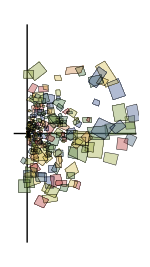

```mathematica
vizHandmap1[
data,
CoordIndex1->-2,
LongitudeRange->{-10Degree,90Degree},
ImageSize->150,
PolygonColorFunc->Function[{x},cf[Random[]]],
PolygonStyleFunc->Function[{x},
{EdgeForm[{Black,Thickness[0.002]}],
FaceForm[Opacity[0.4]]}]
]
```

```mathematica
stats0=rfStats[
data,
CoordIndex1->-2];
```

```mathematica
stats=Map[#[[-2;;-1]]&,stats0];
```

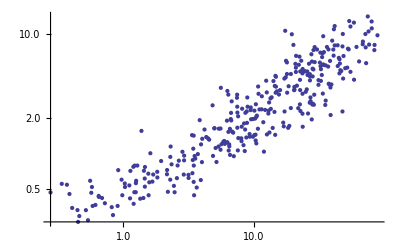

```mathematica
g1=ListLogLogPlot[stats]
```

```mathematica
(* V1 function from Rosa, Fritsches & Elston, 1997 *)
f1[e_]:=E^(Log[0.764]+0.495*Log[e]+0.05*Log[e]^2)
```

```mathematica
(* function from the excel sphreadsheet *)
f3[e_]:=E^(Log[0.49648]+0.6583*Log[e])
```

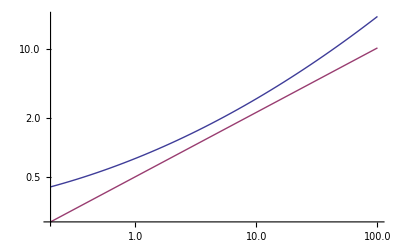

```mathematica
g0=LogLogPlot[{f1[e],f3[e]},{e,0.2,100}]
```

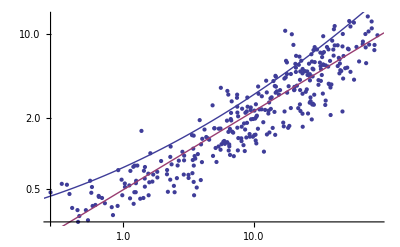

```mathematica
Show[g1,g0]
```